```mathematica
AsymptoticLimiter[x_]:=x/(1+Abs[x])
Distortion[x_]:= 4AsymptoticLimiter[(1/4)(2AsymptoticLimiter[x]-x)]
Effect1[x_]:=8Nest[Distortion,N[4 AsymptoticLimiter[x]],4]
Manipulate[
Plot[{Sin[x],Effect1[2^v Sin[x]]},{x,0,2π}],
{{v,0},-10,10}
]
```

```mathematica
Effect2[x_]:=Sin[x]
Manipulate[
Plot[{Sin[x],Effect2[2^v Sin[x]]},{x,0,2π}],
{{v,0},-10,10}
]
```

```mathematica
soundTest =Table[Effect2[20 2^(-x/16000)(Sin[150 2 π x/48000]+Sin[(3/2)150 2 π x/48000])],{x,1,3 48000}];
```

```mathematica
ListPlay[soundTest,SampleRate->48000]
```

-Graphics-

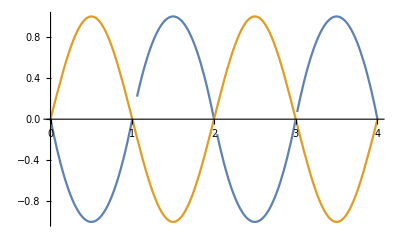

```mathematica
FakeSin[x_]:=Module[{s,sign},
sign = Sign[0.5x - Floor[0.5x]-0.5]; 
s = x - Floor[x];
4(s-s^2)sign
]
Plot[{FakeSin[x],Sin[π x]},{x,0,4}]
```